# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]][[1;;-1]]
```

{C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

## Fehler

```mathematica
σv=0.025;
σP=0.25;
```

## Plotting

{Gas, Gemischt, Flüssig}

```mathematica
colours={RGBColor[0,0.6,0], RGBColor[0.56,0.37,0.60],Blue}
```

{RGBColor[0, 0.6, 0],RGBColor[0.56, 0.37, 0.6],RGBColor[0, 0, 1]}

```mathematica
states={"Gas", "Gemischt","Flüssig"}
```

{Gas,Gemischt,Flüssig}

```mathematica
assoc=AssociationThread[states,colours];
```

```mathematica
cf[_,_,_]=Black;
```

```mathematica
Do[((cf[i,x_,y_]/;(x-#[[1]])^2+(y-#[[2]])^2<=0.01=assoc[#[[3]]])&)/@data[[i]],{i,1,Length[data]}]
```

```mathematica
(*Do[cf[data[[i,j,1]],data[[i,j,2]]]=assoc[data[[i,j,3]]],{i,1,Length[data]},{j,1,Length[data[[i]]]}]*)
```

{Around[#[[1]],σv],Around[#[[2]],σP]} for error bars

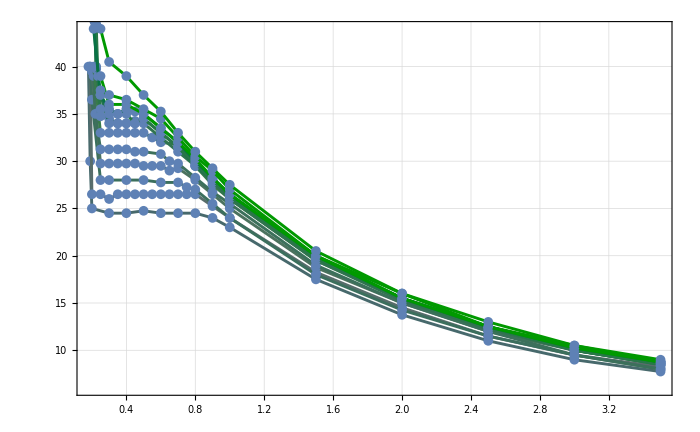

```mathematica
plts=Flatten@Table[{ListPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,Joined->True,pltsettings,PlotStyle->Thickness[0.003]],ListPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,PlotStyle->PointSize[0.01]]},{i,1,Length[data]}];
Show[plts,PlotRange->{Automatic,{6,44}}]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig1.pdf",Show[plts],Background->None];
```

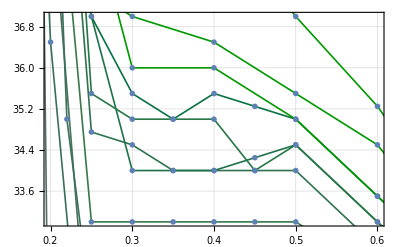

```mathematica
Show[plts,PlotRange->{{0.2,0.6},{33,37}},ImageSize->400]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig1b.pdf",Show[plts,PlotRange->{{0.2,0.6},{33,37}},ImageSize->400],Background->None];
```

```mathematica
loglogplts=Flatten@Table[{ListLogLogPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,Joined->True,pltsettings,PlotStyle->Thickness[0.003]],ListLogLogPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,PlotStyle->PointSize[0.01]]},{i,1,Length[data]}];
```

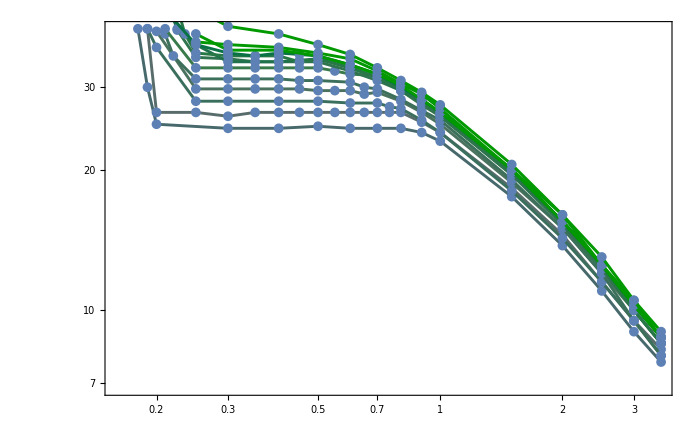

```mathematica
Show[loglogplts,ScalingFunctions->{"Log","Log"}]
```

## Log Log Plots & Fits

P = νRT/V

ln P = log (\nu R T) - log V

```mathematica
logdata=Log[#[[-4;;-1,{1,2}]]]&/@data
```

{{{0.693147,2.62104},{0.916291,2.3979},{1.09861,2.19722},{1.25276,2.04769}},{{0.693147,2.67415},{0.916291,2.44235},{1.09861,2.25129},{1.25276,2.11021}},{{0.693147,2.65676},{0.916291,2.44235},{1.09861,2.25129},{1.25276,2.07944}},{{0.693147,2.70805},{0.916291,2.48491},{1.09861,2.30259},{1.25276,2.14007}},{{0.693147,2.70805},{0.916291,2.48491},{1.09861,2.25129},{1.25276,2.07944}},{{0.693147,2.74084},{0.916291,2.52573},{1.09861,2.32728},{1.25276,2.16905}},{{0.693147,2.72458},{0.916291,2.50553},{1.09861,2.30259},{1.25276,2.14007}},{{0.693147,2.74084},{0.916291,2.52573},{1.09861,2.30259},{1.25276,2.14007}},{{0.693147,2.74084},{0.916291,2.52573},{1.09861,2.30259},{1.25276,2.14007}},{{0.693147,2.74084},{0.916291,2.52573},{1.09861,2.32728},{1.25276,2.16905}},{{0.693147,2.74084},{0.916291,2.52573},{1.09861,2.32728},{1.25276,2.16905}},{{0.693147,2.77259},{0.916291,2.52573},{1.09861,2.35138},{1.25276,2.16905}},{{0.693147,2.77259},{0.916291,2.56495},{1.09861,2.35138},{1.25276,2.19722}}}

```mathematica
LinearModelFit[#,x,x]&/@logdata
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
fitData=LinearModelFit[#,x,x]["ParameterTableEntries"][[1;;2,1]]&/@logdata
```

{{3.33793,-1.03208},{3.37321,-1.01365},{3.37771,-1.03035},{3.41158,-1.0126},{3.50555,-1.13576},{3.45743,-1.02676},{3.4574,-1.04949},{3.50242,-1.08575},{3.50242,-1.08575},{3.45743,-1.02676},{3.45743,-1.02676},{3.5101,-1.06586},{3.50142,-1.04007}}

ln(ν R T) = ln(ν R) + ln (T) in Abhängigkeit von T

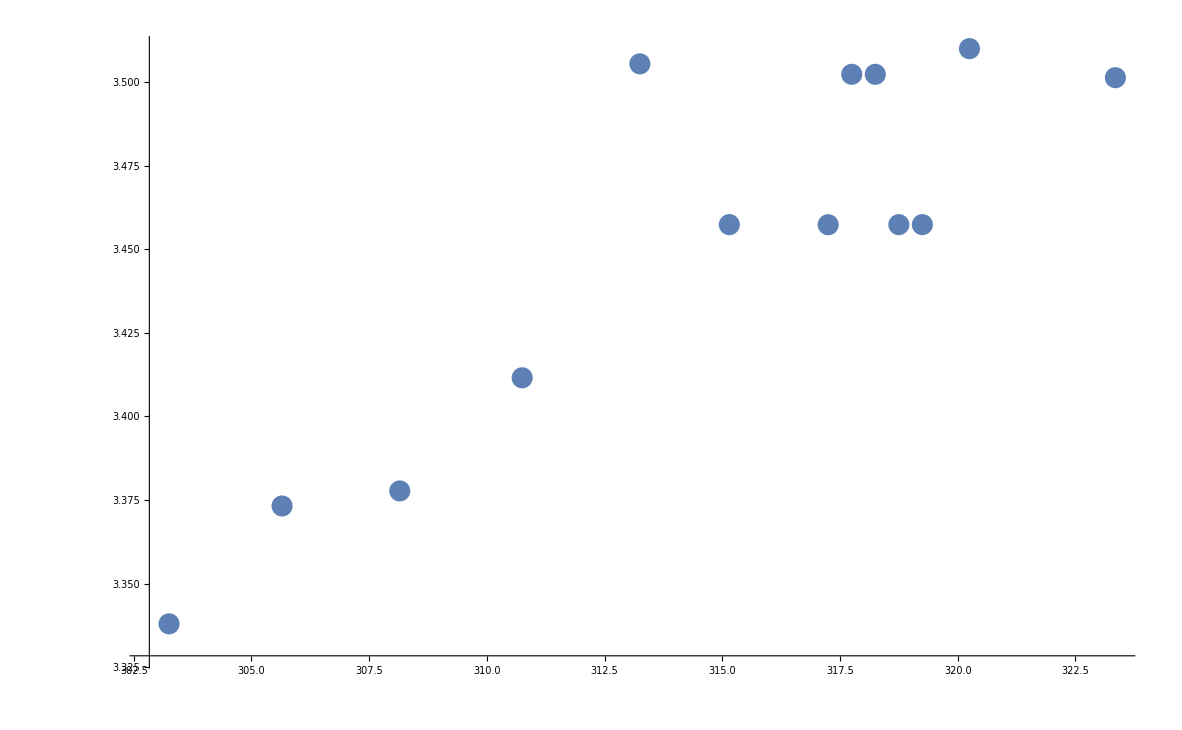

```mathematica
ListPlot[Transpose[{temps+273.15,fitData⟦All,1⟧}]]
```

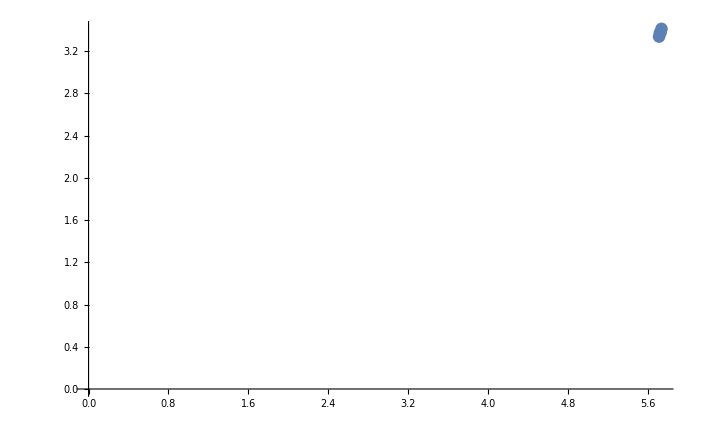

```mathematica
ListPlot[Transpose[{Log[temps+273.15],fitData⟦All,1⟧}][[1;;4]],AxesOrigin->{0,0}]
```

```mathematica
LinearModelFit[Transpose[{Log[temps+273.15],fitData⟦All,1⟧}][[1;;4]],x,x]
```

FittedModel[…]

```mathematica
LinearModelFit[Transpose[{Log[temps+273.15],fitData⟦All,1⟧}],x,x]["ParameterTableEntries"]
```

{{-11.6793,2.40896,-4.84827,0.000512175},{2.63055,0.418842,6.28052,0.0000599838}}

## Fits

```mathematica
FindFit[data[[-1,All,{1,2}]],]
```

FindFit::argrx: FindFit called with 2 arguments; 4 arguments are expected.

FindFit[{{0.25,44.},{0.3,40.5},{0.4,39.},{0.5,37.},{0.6,35.25},{0.7,33.},{0.8,31.},{0.9,29.25},{1.,27.5},{1.5,20.5},{2.,16.},{2.5,13.},{3.,10.5},{3.5,9.}},Null]

## This is the final plot

```mathematica
(*plotMarkers->{Graphics[{Disk[{0,0},Scaled[0.02]]}],Graphics[{Disk[{0,0},Scaled[0.02]]}] }*)
```

```mathematica
plotMarkers=Charting`CommonDump`GraphicsOpenPlotMarkers[][[1;;3]];
```

```mathematica
plotMarkerAssoc=AssociationThread[states,plotMarkers];
```

```mathematica
flattened=Flatten[Map[#[[1;;3]]&, data,{2}],1];
```

```mathematica
pmarkers=plotMarkerAssoc[#[[3]]]&/@flattened;
```

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

```mathematica
pcolours=Flatten[Table[ConstantArray[cols[[i]],Length[data[[i]]]],{i,1,Length[data]}],1];
```

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours]]
```

-Graphics-

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours],PlotRange->{{0.2,0.6},{33,37}}]
```

-Graphics-

```mathematica
data[[-1]],
```

```mathematica
files[[6]]
```

C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx

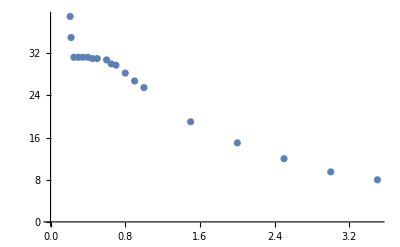

```mathematica
ListPlot[{#[[1]],#[[2]]}&/@data[[5]]]
```

## Log P Plot

```mathematica
V0=0.4
```

0.4

```mathematica
pvals=Flatten[DeleteCases[x_/;x[[1]]!=V0]/@data,1]
```

{{0.4,24.5,Gemischt},{0.4,26.5,Gemischt},{0.4,28.,Gemischt},{0.4,29.75,Gemischt},{0.4,31.25,Gemischt},{0.4,33.,Gemischt},{0.4,34.,Gemischt},{0.4,34.,Gemischt},{0.4,35.,Gemischt},{0.4,35.5,Gas},{0.4,36.,Gas},{0.4,36.5,Gas},{0.4,39.,Gas}}

```mathematica
data2=Transpose[{temps, pvals[[All,2]]}]
```

{{30.1,24.5},{32.5,26.5},{35.,28.},{37.6,29.75},{40.1,31.25},{42.,33.},{44.1,34.},{44.6,34.},{45.1,35.},{45.6,35.5},{46.1,36.},{47.1,36.5},{50.2,39.}}

```mathematica
data2plot={1/#[[1]],Log[#[[2]]]}&/@data2;
```

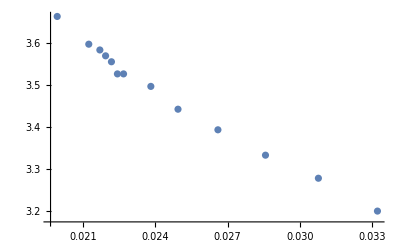

```mathematica
ListPlot[data2plot]
```